1

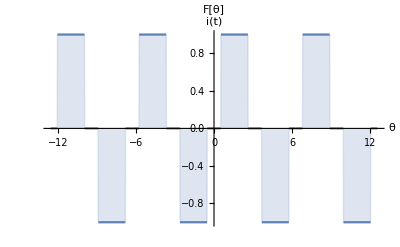

```mathematica
Clear["Global`*"]
(*Función*)
T= 2π;
Ttemporal =T/(2π)
duty = 1/2;
(*F[θ_] := 2*UnitBox[Mod[variable/T,1.]/(2. duty)]-1*)
Faux[θ_] := UnitStep[θ-π/6]- UnitStep[θ - (π-π/6)]- UnitStep[θ-(π+π/6)]+UnitStep[θ-(π+π/6+(2π)/3)]
F[θ_]:= Faux[Mod[θ,T,0]]
Plot[{F[θ]},{θ,-4π,4π}, PlotLabel->"F[θ]",AxesLabel->{"θ","i(t)"},Filling->Axis]
```

```mathematica
(*Gráfico de la función*)
```

Valor RMS de F[θ]: 0.816497

Valor RMS del Armonico h: (√2 √((Cos[(h π)/6]-Cos[(5 h π)/6])^2/h^2))/π

Valor RMS de la fundamental 0.779697

Corriente de distorsión: -(2 √3 Sin[t])/π+UnitStep[-(11 π)/6+Mod[2 π t,2 π,0]]-UnitStep[-(7 π)/6+Mod[2 π t,2 π,0]]-UnitStep[-(5 π)/6+Mod[2 π t,2 π,0]]+UnitStep[-π/6+Mod[2 π t,2 π,0]]

Valor RMS de la corriente de distorsión: 0.242362

THD: 31.0842

Factor de potencia: 0.95493 Cos[ϕ]

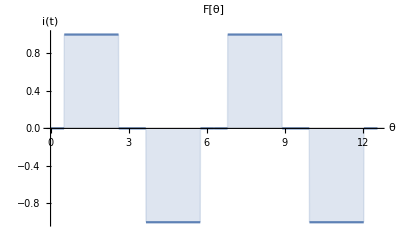

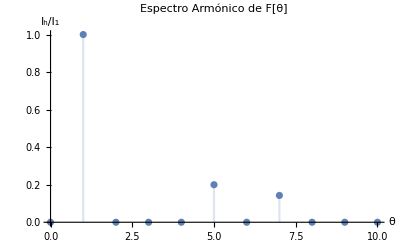

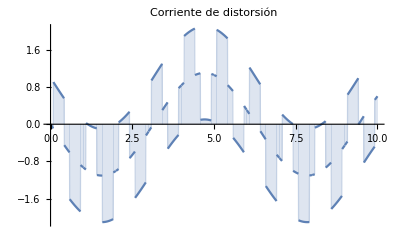

```mathematica
(*Análisis Armónico*)
RMSF = √(1/T∫_(-T/2)^(T/2) F[θ]^2 ⅆθ);
ah[h_]:= 1/π∫_-π^π (F[θ]*Cos[h*θ])ⅆθ
bh[h_]:=1/π∫_-π^π (F[θ]*Sin[h*θ])ⅆθ

serieFourier[θ_,n_]:= 1/2∫_-π^π F[θ]ⅆθ + ∑_(h=1)^n (ah[h]*Cos[h*θ] + bh[h]*Sin[h*θ])
RMSh[h_]:=(√(ah[h]^2+bh[h]^2))/(√2)


FullSimplify[ah[h]];
FullSimplify[bh[h]];

iDis = F[(2π)/Ttemporal*t] - FourierSeries[F[t],t,1];
RMSiDis = √(RMSF^2-RMSh[1]^2);
THDi = 100*(RMSiDis/RMSh[1]);
DPF = "Por implementar";
PF = RMSh[1]/RMSF*Cos[ϕ];


(*Salida datos*)
Print["Valor RMS de F[θ]: ", RMSF//N]
Print["Valor RMS del Armonico h: ", FullSimplify[RMSh[h]]]
Print["Valor RMS de la fundamental ", FullSimplify[RMSh[1]]//N]
Print["Corriente de distorsión: ", FullSimplify[iDis]]
Print["Valor RMS de la corriente de distorsión: ", RMSiDis//N]
Print["THD: ", THDi//N]
Print["Factor de potencia: ", PF//N]
Plot[{F[θ]},{θ,0,4π}, PlotLabel->"F[θ]",AxesLabel->{"θ","i(t)"},Filling->Axis]
DiscretePlot[RMSh[h]/RMSh[1],{h,0,10},PlotLabel->"Espectro Armónico de F[θ]", PlotRange->Full, AxesLabel->{"θ","I_h/I_1"}]
Plot[iDis,{t, 0,10},PlotRange->All, PlotLabel->"Corriente de distorsión",Filling->Axis]
```